# IPPT Model

## 3d. 2-Set Data Import, Single Pulse

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice using two input files.
- Results are imported from WDX format from desired file path on PC.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice. Export data using 3b to create a WDX file type.
- Pull the desired three files to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the files were produced and the shot numbers to reflect desired data sources

```mathematica
Filedate1 = "2021-09-07";
Filedate2 = "2022-02-13";
Shotnum1 = "3"; 
Shotnum2 = "19";
Codeversion = "1.12";

filename1 = StringJoin[Filedate1,"_v",Codeversion,"_run_",Shotnum1,".wdx"];
shotdata1 = Import[filename1];
filename2 = StringJoin[Filedate2,"_v",Codeversion,"_run_",Shotnum2,".wdx"];
shotdata2 = Import[filename2];
```

## Unpack Data

```mathematica
tmaxt1 = shotdata1[[3]];
tmaxt2 = shotdata2[[3]];

χi0t1=shotdata1[[7]];
znt1 = shotdata1[[10]];
Lct1=shotdata1[[13]];
L0t1=shotdata1[[14]];
C0t1=shotdata1[[16]];
zct1 = shotdata1[[18]];
χi0t2=shotdata2[[7]];
znt2=shotdata2[[10]];
Lct2=shotdata2[[13]];
L0t2=shotdata2[[14]];
C0t2=shotdata2[[16]];
zct2 = shotdata2[[18]];

τLC1=N[2π(C0t1 Lct1)^(1/2)];
τLC2=N[2π(C0t2 Lct2)^(1/2)];

nn1=shotdata1[[24]];
ws1=shotdata1[[25]];
zs1=shotdata1[[26]];
vs1=shotdata1[[27]];
vf1=shotdata1[[28]];
ns1=shotdata1[[29]];
nf1=shotdata1[[30]];
Ic1=shotdata1[[31]];
Ip1=shotdata1[[32]];
M1=shotdata1[[33]];
V1=shotdata1[[34]];
Te1=shotdata1[[35]];
Ti1=shotdata1[[36]];
ps1=shotdata1[[37]];
KEs1=shotdata1[[38]];
Ef1=shotdata1[[39]];
mbit1=shotdata1[[40]];
ms1[t_]=shotdata1[[41]];
Epi1=shotdata1[[42]];
Eel1=shotdata1[[43]];
Eind1[t_]=shotdata1[[44]];
Ecap1[t_]=shotdata1[[45]];
Eke1[t_]=shotdata1[[46]];
EkePl1[t_]=shotdata1[[47]];
EkeEnt1[t_]=shotdata1[[48]];
Ete1[t_]=shotdata1[[49]];
Ibit1[t_]=shotdata1[[50]];
Isp1[t_]=shotdata1[[51]];
ηm1[t_]=shotdata1[[52]];
MassFrac1[t_]=shotdata1[[53]];
ηT1[t_]=shotdata1[[54]];
ηTrec1[t_]=shotdata1[[55]];
Πiont1[t_]=shotdata1[[56]];
Πiont21[t_]=shotdata1[[57]];
Πcext21[t_]=shotdata1[[58]];

nn2=shotdata2[[24]];
ws2=shotdata2[[25]];
zs2=shotdata2[[26]];
vs2=shotdata2[[27]];
vf2=shotdata2[[28]];
ns2=shotdata2[[29]];
nf2=shotdata2[[30]];
Ic2=shotdata2[[31]];
Ip2=shotdata2[[32]];
M2=shotdata2[[33]];
V2=shotdata2[[34]];
Te2=shotdata2[[35]];
Ti2=shotdata2[[36]];
ps2=shotdata2[[37]];
KEs2=shotdata2[[38]];
Ef2=shotdata2[[39]];
mbit2=shotdata2[[40]];
ms2[t_]=shotdata2[[41]];
Epi2=shotdata2[[42]];
Eel2=shotdata2[[43]];
Eind2[t_]=shotdata2[[44]];
Ecap2[t_]=shotdata2[[45]];
Eke2[t_]=shotdata2[[46]];
EkePl2[t_]=shotdata2[[47]];
EkeEnt2[t_]=shotdata2[[48]];
Ete2[t_]=shotdata2[[49]];
Ibit2[t_]=shotdata2[[50]];
Isp2[t_]=shotdata2[[51]];
ηm2[t_]=shotdata2[[52]];
MassFrac2[t_]=shotdata2[[53]];
ηT2[t_]=shotdata2[[54]];
ηTrec2[t_]=shotdata2[[55]];
Πiont2[t_]=shotdata2[[56]];
Πiont22[t_]=shotdata2[[57]];
Πcext22[t_]=shotdata2[[58]];

(* Calculate non-imported energy fraction *)
EnergyFrac1[t_]=(Eke1[t]+KEs1[t])/(Eel1+Epi1-Ecap1[t]);
EnergyFrac2[t_]=(Eke2[t]+KEs2[t])/(Eel2+Epi2-Ecap2[t]);
```

## Characteristic Ambient Neutral Length Scale Comparison, Rev 1

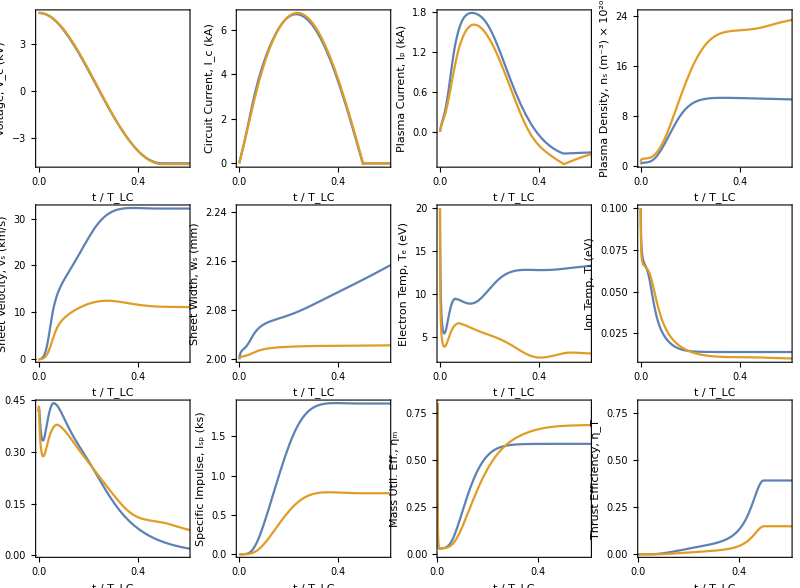

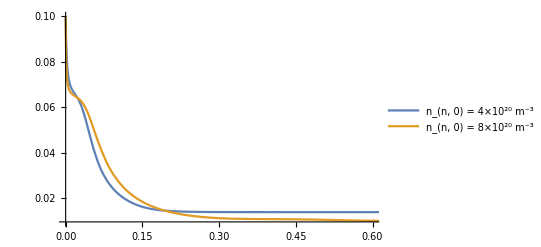

```mathematica
ZnPlot[Fun1_,Fun2_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
ZnkPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffZnPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0.01,0.6},{0,0.8}},
(* PlotStyle->{{DotDashed,Black},{Dashed,Black},{Dotted,Black},{Black}}, *)
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** IEPC Output **)
Print[GraphicsGrid[{
{ZnPlot[V1,V2,"Voltage, V_c (kV)",10^-3],ZnPlot[Ic1,Ic2,"Circuit Current, I_c (kA)",10^-3],ZnPlot[Ip1,Ip2,"Plasma Current, I_p (kA)",10^-3],ZnPlot[ns1,ns2,"Plasma Density, n_s (m^-3) × 10^20",10^-20]},
{ZnPlot[vs1,vs2,"Sheet Velocity, v_s (km/s)",10^-3],ZnPlot[ws1,ws2,"Sheet Width, w_s (mm)",10^3],ZnPlot[Te1,Te2,"Electron Temp, T_e (eV)",1],ZnPlot[Ti1,Ti2,"Ion Temp, T_i (eV)",1]},
{ZnkPlot[M1,M2,"Coupling Coefficient, k",1],ZnPlot[Isp1,Isp2,"Specific Impulse, I_sp (ks)",10^-3],EffZnPlot[ηm1,ηm2,"Mass Util. Eff., η_m",1],EffZnPlot[ηTrec1,ηTrec2,"Thrust Efficiency, η_T",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(* Produce Legend *)
Plot[{Ti1[Τ τLC1],Ti2[Τ τLC2]},{Τ,0,1},
PlotRange-> {{0,0.6},All},PlotLegends-> {"n_(n, 0) = 4×10^20 m^-3","n_(n, 0) = 8×10^20 m^-3"},LabelStyle->{16,Black,FontFamily->"Times"}]
```

## Thesis Formatting, Propellant Comparison, Rev 1

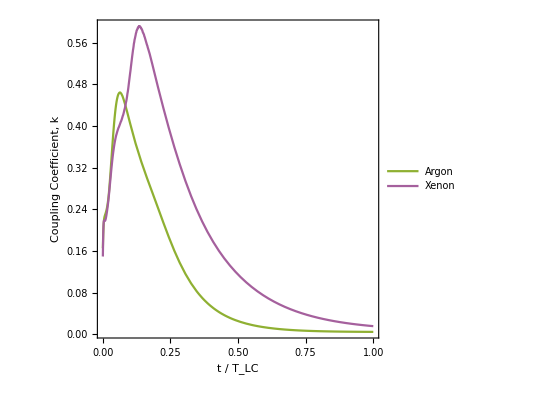

General::munfl: Exp[-7.13398×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.39648×10^7] is too small to represent as a normalized machine number; precision may be lost.

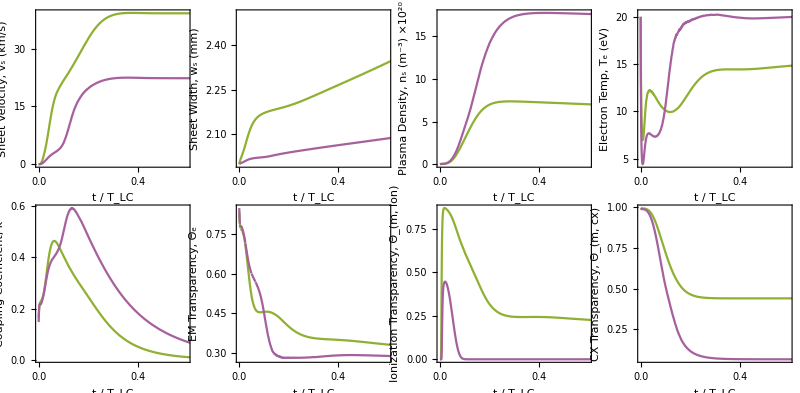

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lct1 scale,Fun2[Τ τLC2]/Lct2 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Transparency Calculations **)
za=-0.002; 
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    

SionAr[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcxAr= 5 10^-19;
σenAr=4 10^-20;  
SionXe[Te_]:= 10^-20 (-0.0001031 Te^2+6.386 Exp[-12.127/Te])(8ec Te/(π me))^(1/2); (* Xenon *)
σcxXe= 7.5 10^-19;
σenXe=5 10^-20; 

ΛAr[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiAr[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛAr[ne,Te]  (* e-i collision frequency *)
νenAr[nn_,Te_]:=nn σenAr ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclAr[ne_,nn_,Te_]:=(me (νeiAr[ne,Te]+νenAr[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdAr[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclAr[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)
ΛXe[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiXe[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛXe[ne,Te]  (* e-i collision frequency *)
νenXe[nn_,Te_]:=nn σenXe((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclXe[ne_,nn_,Te_]:=(me (νeiXe[ne,Te]+νenXe[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdXe[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclXe[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsdAr[L0t1+Lct1-M1[t]^2/Lct1,C0t1,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δs2[t_]=δsdXe[L0t2+Lct2-M2[t]^2/Lct2,C0t2,ns2[t],nn2[zs2[t],t]+nf2[t],Te2[t]];

Θs1[t_]=Exp[-3ws1[t]/δs1[t]];
Θs2[t_]=Exp[-3ws2[t]/δs2[t]];

Θmion1[t_]=Exp[(-ns1[t]ws1[t]SionAr[Te1[t]])/vs1[t]];
Θmion2[t_]=Exp[(-ns2[t]ws2[t]SionXe[Te2[t]])/vs2[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcxAr];
Θmcex2[t_]=Exp[-ns2[t] ws2[t]σcxXe];

(** Legend Generator **)
Plot[{M1[Τ τLC1]/Lct1,M2[Τ τLC2]/Lct2},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"Argon", "Xenon"},
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Journal Output **)
Print[GraphicsGrid[{
{JPlot[vs1,vs2,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[ws1,ws2,"Sheet Width, w_s (mm)",10^3],JPlot[ns1,ns2,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Te1,Te2,"Electron Temp, T_e (eV)",1]},
{JkPlot[M1,M2,"Coupling Coefficient, k",1],JPlot[Θs1,Θs2,"EM Transparency, Θ_e",1],JPlot[Θmion1,Θmion2,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcex1,Θmcex2,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```